```mathematica
Integrate[(2/L)*(Sin[n*Pi*x/L])^2*((1/A)*x^ξ),{x,0,L}]


pertubation1=(2 L^ξ (-2 n^2 π^2 HypergeometricPFQ[{3/2+ξ/2},{3/2,5/2+ξ/2},-n^2 π^2]))/(A (1+ξ) (3+ξ))//N
```

-(2.50867×10^-19 (1.×10^9)^(-1. ξ) n^2 HypergeometricPFQ[{1.5+0.5 ξ},{1.5,2.5+0.5 ξ},-9.8696 n^2])/((1.+ξ) (3.+ξ))

```mathematica
-(2.50867*10^(-19) *10^(9-ξ) n^2 HypergeometricPFQ[{1.5+0.5 ξ},{1.5,2.5+0.5 ξ},-9.8696*n^2])/((1+ξ) (3+ξ))
pertubation1/.n->1//Simplify;A=(2*0.511*10^6)/(6.58211*10^(-16))^2//N;
L=10^-9//N;
```

-(2.50867×10^-19 ⅇ^(-20.7233 ξ) HypergeometricPFQ[{1.5+0.5 ξ},{1.5,2.5+0.5 ξ},-9.8696])/(3.+4. ξ+ξ^2)

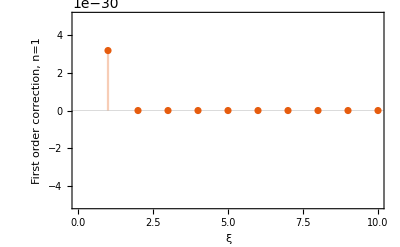

```mathematica
DiscretePlot[pertubation1/.n->1,{ξ,1,10},PlotRange->{-5*10^(-30),5*10^(-30)},Frame->True,FrameLabel->{"ξ","First order correction, n=1"},PlotTheme->"Scientific"]
```

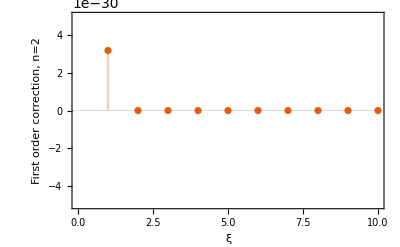

```mathematica
DiscretePlot[pertubation1/.n->2,{ξ,1,10},PlotRange->{-5*10^(-30),5*10^(-30)},Frame->True,FrameLabel->{"ξ","First order correction, n=2"},PlotTheme->"Scientific"]
```

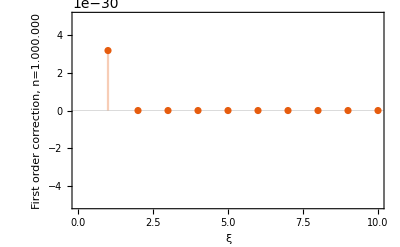

```mathematica
DiscretePlot[pertubation1/.n->1000000,{ξ,1,10},PlotRange->{-5*10^(-30),5*10^(-30)},Frame->True,FrameLabel->{"ξ","First order correction, n=1.000.000"},PlotTheme->"Scientific"]
```

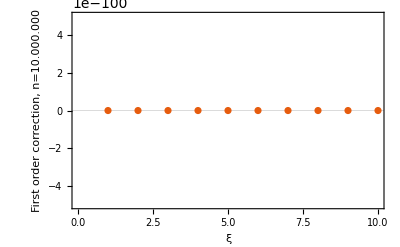

```mathematica
DiscretePlot[pertubation1/.n->10000000,{ξ,1,10},PlotRange->{-5*10^(-100),5*10^(-100)},Frame->True,FrameLabel->{"ξ","First order correction, n=10.000.000"},PlotTheme->"Scientific"]
```

```mathematica
(*The same results could be obtained if we ploted without DiscretePlot but in this case ξ is no more an integer*)


pertubation1nfunction[n_]:=(2 L^ξ (-2 n^2 π^2 HypergeometricPFQ[{3/2+ξ/2},{3/2,5/2+ξ/2},-n^2 π^2]))/(A (1+ξ) (3+ξ))
```

```mathematica
pertubation1nfunction[1]
```

-(2.50867×10^-19 1000000000^-ξ HypergeometricPFQ[{3/2+ξ/2},{3/2,5/2+ξ/2},-π^2])/((1+ξ) (3+ξ))

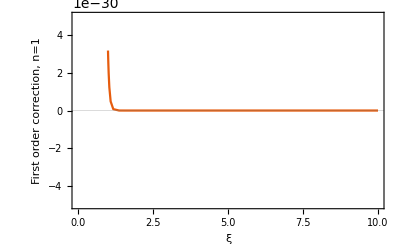

```mathematica
Plot[-(2.508668429150692*^-19 1000000000^-ξ HypergeometricPFQ[{3/2+ξ/2},{3/2,5/2+ξ/2},-π^2])/((1+ξ) (3+ξ)),{ξ,1,10},PlotRange->{-5*10^(-30),5*10^(-30)},Frame->True,FrameLabel->{"ξ","First order correction, n=1"},PlotTheme->"Scientific"]
```

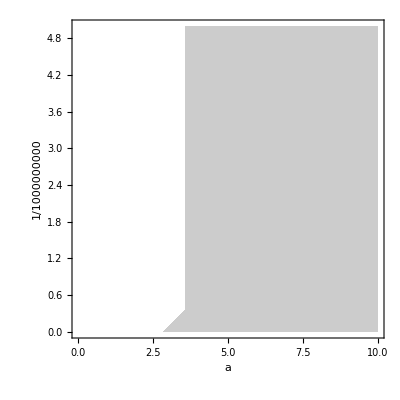

```mathematica
ContourPlot[pertubation1,{ξ,0,10},{n,0,5},FrameLabel->{a,L}, PlotLegends->Automatic,ColorFunction->"Rainbow"]
```